Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 6 Gerschgorin disks
Find and sketch disks or intervals that contain the eigenvalues. If you have a CAS, find the spectrum and compare.

I found a couple of Gerschgorin disk makers on-line. The one I decided worked best for me was at http://distrustsimplicity.net/articles/gerschgorin-disks/. It is a Show command made up of a plot and a graphic. In the original version the ListPlot is called first, but since the ListPlot doesn’t use all the space needed for the graphic, yet has the primacy of being called first, a truncated window is the result. By switching it around so that the graphic is called first, I get to see everything.

```mathematica
GerschgorinPlot[A_]:=(*Store the number of rows in A*)With[{n=Dimensions[A][[1]]},Show[(*Create a translucent gray disk for each row*){Graphics[{{EdgeForm[Thin],GrayLevel[0.1,0.1],Disk[{Re[#1],Im[#1]},#2]},{}},{Axes->True}]}&@@@Thread[{(*Disk centers*)Table[A[[i,i]],{i,1,n}],(*Disk radii*)Table[Total[Abs[A[[i]]],i]-Abs[A[[i,i]]],{i,1,n}]}],
(*Plot the eigenvalues as points*)
ListPlot[{Re[#],Im[#]}&/@Eigenvalues[A],AxesOrigin->{0,0},AspectRatio->Automatic,PlotRange->All,PlotStyle->{Black,PointSize[Medium]}]
]]
```

1.  (5 | 2 | 4
-2 | 0 | 2
2 | 4 | 7)

```mathematica
m1={{5, 2, 4}, {-2, 0, 2}, {2, 4, 7}}
```

{{5,2,4},{-2,0,2},{2,4,7}}

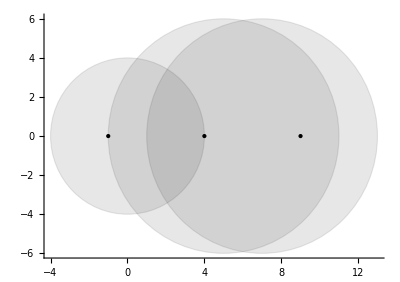

```mathematica
GerschgorinPlot[m1]
```

```mathematica
Eigenvalues[m1]
```

{9,4,-1}

The text answer gives the circle centers {5,0,7}, the circle respective radii {6,4,6}, and the Spectrum {-1,4,9}. However, if the spectrum list is also to match eigenvalues with the circles they most apparently internalize, the spectrum order would be {4,-1,9}.

3.  (0 | 0.4 | -0.1
-0.4 | 0 | 0.3
0.1 | -0.3 | 0)

```mathematica
m2={{0, 0.4, -0.1}, {-0.4, 0, 0.3}, {0.1, -0.3, 0}}
```

{{0,0.4,-0.1},{-0.4,0,0.3},{0.1,-0.3,0}}

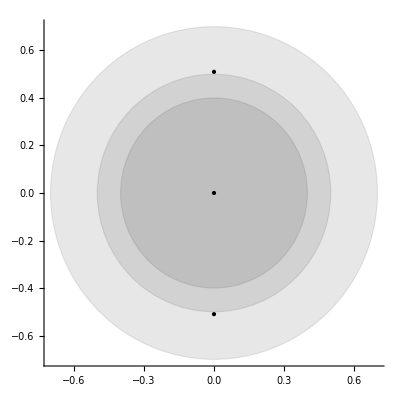

```mathematica
GerschgorinPlot[m2]
```

```mathematica
Eigenvalues[m2]
```

{0.+0.509902 ⅈ,0.-0.509902 ⅈ,-5.37807×10^-18+0. ⅈ}

The text answers gives circle centers as 0, with radii {0.5,0.7,0.4}

The text identifies eigenvalues as belonging to a continuous line on the imaginary axis, from -0.7ⅈ to 0.7ⅈ, apparently as an attribute of a skew-symmetric matrix. I do admit that the graphic above looks strange, in that the central disk doesn’t seem to have much purpose.

5.  (2 | ⅈ | 1+ⅈ
-ⅈ | 3 | 0
1-ⅈ | 0 | 8)

```mathematica
m3={{2, ⅈ, 1+ⅈ}, {-ⅈ, 3, 0}, {1-ⅈ, 0, 8}}
```

{{2,ⅈ,1+ⅈ},{-ⅈ,3,0},{1-ⅈ,0,8}}

```mathematica
Abs[ⅈ]
```

1

```mathematica
Abs[1+ⅈ]
```

√2

```mathematica
Abs[1-ⅈ]
```

√2

```mathematica
data={{3+√2,0},{8+√2,0}}
```

{{3+√2,0},{8+√2,0}}

```mathematica
p1=ListPlot[data, PlotStyle->Orange];
```

```mathematica
p2=GerschgorinPlot[m3];
```

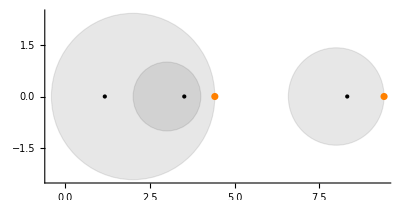

```mathematica
Show[p2,p1]
```

```mathematica
N[Eigenvalues[m3]]
```

{8.32584,3.51108,1.16308}

Centers at {2,3,8}, radii of {1+√2,1,√2}

7.  Similarity. In problem 2, find T^-TAT such that the radius of the Gerschgorin circle with center 5 is reduced by a factor 1/100.

```mathematica
Clear["Global`*"]
```

This problem follows example 2, p. 881 closely. The radius is currently 2×10^-2 . The problem has targeted the first row for reduction by 1/100, meaning that final desired radius is 0.02*0.01=0.0002.

```mathematica
biga=({{5, 10^-2, 10^-2}, {10^-2, 8, 10^-2}, {10^-2, 10^-2, 9}})
```

{{5,1/100,1/100},{1/100,8,1/100},{1/100,1/100,9}}

For this problem I don’t need the eigenvalues, but I called for them, and they don’t take up a lot of space.

```mathematica
N[Eigenvalues[biga]]
```

{9.00013,7.99993,4.99994}

Just to get a feel for the double dot setup, I’ll try an identity matrix multiplication.

```mathematica
bigt=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
```

{{1,0,0},{0,1,0},{0,0,1}}

The double dot multiplication leaves the original matrix unchanged, which is reassuring.

```mathematica
Inverse[bigt].biga.bigt
```

{{5,1/100,1/100},{1/100,8,1/100},{1/100,1/100,9}}

In example 2 the diagonal member of the T matrix associated with the targeted radius in A was increased by 5 decimals, which reduced the targeted radius by 5 decimals. I want to reduce by 2 decimals, so I will adjust the diagonal like so, since the 5-centered circle I want to affect is on the top row.

```mathematica
bigt2=({{100, 0, 0}, {0, 1, 0}, {0, 0, 1}})
```

{{100,0,0},{0,1,0},{0,0,1}}

The top radius is reduced.

```mathematica
Inverse[bigt2].biga.bigt2
```

{{5,1/10000,1/10000},{1,8,1/100},{1,1/100,9}}

And looked at decimalwise.

```mathematica
N[1/10000+1/10000]
```

0.0002

The matrix bigt2 does what is asked.

9.  If a symmetric n×n matrix A = [a_jk] has been diagonalized except for small off-diagonal entries of size 10^-5 , what can you say about the eigenvalues?

This problem is a revisitation of example 1 on p. 880. If the matrix A were diagonal, the entries on the diagonal would be the eigenvalues. Since it is not diagonal, the Gorschgorin circles are error bounds to the locations of the eigenvalues, which lie on the x-axis if I am in ℝ. If the off-diagonal values are of order 10^-5 it means that the Gorschgorin radii are of order 2 × 10^-5, and the error bounds around the eigenvalues can be duly calculated. However, this is so even if the matrix is not symmetrical. I think I am missing something here.

11.  Spectral radius ρ(A).
Using theorem 1, show that ρ(A) cannot be greater than the row sum norm of A.

Suppose I have a 3 × 3 matrix A and that {a, b, c} is a row of A, the row which contains the center of the Gorschgorin disk that contains the largest eigenvalue of A. So that

```mathematica
aye={a,b,c}
```

{a,b,c}

and

```mathematica
bn=Norm[aye,1]
```

Abs[a]+Abs[b]+Abs[c]

If the element of ‘aye’ which is the disk center happens to be at the origin, and the eigenvalue in that disk, (which is the max eigenvalue), happens to lie on the circumference of the disk, then the spectral radius is equal to bn; otherwise, the spectral radius is less than bn, because then the eigenvalue will be less than the disk radius. Also the spectral radius is less than bn if the disk center is not at the origin, because then bn will be even larger. (This loose argument, which could be generalized to n × n matrices, does not depend on theorem 1 as far as I know.)

12 - 16 Spectral radius
Use (4) to obtain an upper bound for the spectral radius:

13. In problem 1.
15. In problem 2.

13. Numbered line (4) on p. 882 contains Schur’s inequality.

```mathematica
Clear["Global`*"]
```

```mathematica
m1={{5, 2, 4}, {-2, 0, 2}, {2, 4, 7}}
```

{{5,2,4},{-2,0,2},{2,4,7}}

```mathematica
flb=Flatten[m1]
```

{5,2,4,-2,0,2,2,4,7}

```mathematica
N[Sum[Abs[flb[[n]]]^2,{n,1,9}]]
```

122.

```mathematica
Sqrt[%]
```

11.0454

The logical check to this is

```mathematica
Eigenvalues[m1]
```

{9,4,-1}

15. Schur’s again.

```mathematica
Clear["Global`*"]
```

```mathematica
m2=({{0, 0.4, -0.1}, {-0.4, 0, 0.3}, {0.1, -0.3, 0}})
```

{{0,0.4,-0.1},{-0.4,0,0.3},{0.1,-0.3,0}}

```mathematica
flab=Flatten[m2]
```

{0,0.4,-0.1,-0.4,0,0.3,0.1,-0.3,0}

```mathematica
N[Sum[Abs[flab[[n]]]^2,{n,1,9}]]
```

0.52

```mathematica
Sqrt[%]
```

0.72111

and

```mathematica
Eigenvalues[m2]
```

{0.+0.509902 ⅈ,0.-0.509902 ⅈ,-5.37807×10^-18+0. ⅈ}

which although effective, is not as clear-cut as I would like.